```mathematica
x 3
```

```mathematica
y={0,0,1,0,0};
Fx={0,0.3,0.6,0,0};
```

```mathematica
LogisticTransform[x__,k_]:=Exp[x[[k]]]/Total[Exp[x]];
```

```mathematica
Table[LogisticTransform[Fx,k],{k,Length[Fx]}]
```

{0.162023,0.218708,0.295224,0.162023,0.162023}

## 连续函数的Logistic变换

```mathematica
LogisticTransform[f_]:=Exp[f[#]]/(∫_0^1 Exp[f[t]]ⅆt)&;
```

```mathematica
f[x_]:=x;
```

```mathematica
LogisticTransform[f][x]
```

ⅇ^x/(-1+ⅇ)

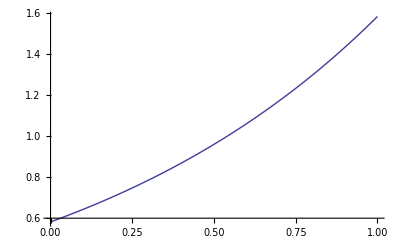

```mathematica
Plot[LogisticTransform[f][x],{x,0,1}]
```